## Коротко о списках

## Создание списков

### Список задаётся фигурными скобками. Его элементы перечисляются внутри через запятую. Элементом списка может быть что угодно.

```mathematica
{1, 2., x+y, RandomColor[]}
```

{1,2.,x+y,RGBColor[0.1033897551318903, 0.42879083287541575, 0.9691769869885447]}

### Есть ряд функций, которые генерируют списки. Например, Range генерирует арифметические прогрессии. Range[n] = {1, 2, ..., n} Range[m, n] = {m, ..., n} Range[start, stop, step] --- арифметическая прогрессия

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Range[5,10]
```

{5,6,7,8,9,10}

```mathematica
Range[0, 1,1/10]
```

{0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1}

### Table позволяет делать что-то наподобие циклов for Table[expr, n] --- n копий

```mathematica
Table[x,3]
```

{x,x,x}

```mathematica
Table[RandomColor[],3]
```

{RGBColor[0.5506562142795115, 0.8494370721470175, 0.8621132610179105],RGBColor[0.29341229591561446, 0.391916908834532, 0.10923681073885749],RGBColor[0.08554627370917034, 0.4045282337665781, 0.33700267970348796]}

### Table[expr, {i, n}] --- список, где i пробегает от 1 до n Все правила из Range перетекают из сюда

```mathematica
Table[x^i,{i,0,5}]
```

{1,x,x^2,x^3,x^4,x^5}

```mathematica
Table[Sin[x],{x, 0, 2π, π/2}]
```

{0,1,0,-1,0}

### Некоторые функции автоматически применяются поэлементно к спискам

```mathematica
x=Range[0, 2π, π/2];
Sin[x]
```

{0,1,0,-1,0}

## Функции

### f[x_]:=выражение, содержащее x f[x_, y_]:=выражение, содержащее x и y f --- имя функции [...] --- список параметров функции Параметры слева указываются с нижним подчеркиванием. Справа --- без.



```mathematica
Clear[x];
f[r_]:=r^2
Plot[f[r], {r,-2, 2}]
```

### Три способа вызвать функцию f с одним аргументом x:

f[x]

f@x

x // f

```mathematica
x=-2;
f[x]
f@x
x//f
```

4

4

4

### Функции большего количества аргументов обычно вызываются в первой форме

```mathematica
g[x_,y_]:=x^2+y^2
Plot3D[g[x,y],{x,-1,1}, {y,-1,1}]
```

-Graphics3D-

### Аргументом может быть что угодно, в том числе и другое выражение

```mathematica
f[√(x^2+y^2)]
```

0.418915

### = --- мгновенное присваивание (Set) := --- Отложенное присваивание (SetDelayed)

```mathematica
samerandom=RandomColor[];
{samerandom, samerandom, samerandom}
```

{RGBColor[0.4293734660174948, 0.5475457377100978, 0.22795811802849242],RGBColor[0.4293734660174948, 0.5475457377100978, 0.22795811802849242],RGBColor[0.4293734660174948, 0.5475457377100978, 0.22795811802849242]}

```mathematica
newrandom :=RandomColor[];
{newrandom, newrandom, newrandom}
```

{RGBColor[0.44113950947421143, 0.2998866530304747, 0.8939324538039279],RGBColor[0.04677224663900681, 0.1759808806158465, 0.14282600879878915],RGBColor[0.44733571955307516, 0.4191386953253764, 0.48118550419442063]}

```mathematica
Clear["Global`*"]
```

### Кусочно-линейные функции Piecewise или lhs := rhs /; test

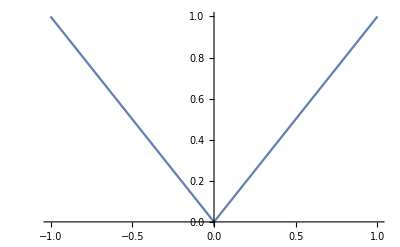

```mathematica
f[x_]:=Piecewise[{{x, x>0}, {-x, x<0}},x]
Plot[f[x],{x,-1,1}]
```

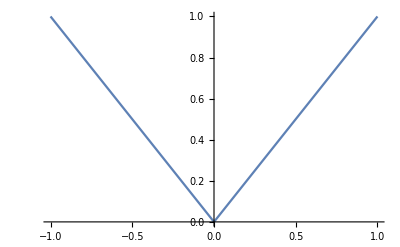

```mathematica
Clear[f]
f[x_]:=x/;x≥0
f[x_]:=-x/;x<0
Plot[f[x],{x,-1,1}]
```

```mathematica
Definition[f]
```

f[x_]:=x/;x≥0
 
f[x_]:=-x/;x<0

### У функции может быть несколько определений.

```mathematica
fib[1]:=1
fib[2]:=1
fib[n_]:=fib[n-1] + fib[n-2]
fib[10]
Definition[fib]
```

55

fib[1]:=1
 
fib[2]:=1
 
fib[n_]:=fib[n-1]+fib[n-2]

```mathematica
Clear[fib]
fib[1]=1;
fib[2]=1;
fib[n_]:=fib[n]=fib[n-1]+fib[n-2]
fib[5]
Definition[fib]
```

5

fib[1]=1
 
fib[2]=1
 
fib[3]=2
 
fib[4]=3
 
fib[5]=5
 
fib[n_]:=fib[n]=fib[n-1]+fib[n-2]

## Преобразование выражений

```mathematica
1-x+24+x y+x
```

25+x y

```mathematica
(2a b)/(b c)
```

(2 a)/c

## Раскрытие скобок и разложение на множители

### Expand и Factor

```mathematica
Clear["Global`*"]
(a+b)(b+c)(c+d)
```

(a+b) (b+c) (c+d)

```mathematica
Expand[%]
```

a b c+b^2 c+a c^2+b c^2+a b d+b^2 d+a c d+b c d

```mathematica
Factor[f[x]]
```

3 (-4+x) (-1+x) (1+x+x^2)

```mathematica
Expand[factor]
```

factor

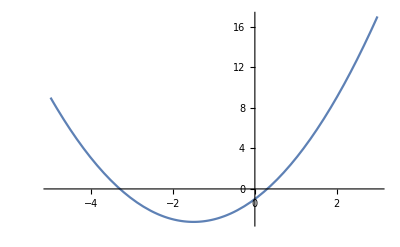

-1+3 x+x^2

```mathematica
Plot[-1+3x + x^2,{x, -5, 3}]
Factor[-1+3x+x^2]
```

```mathematica
Factor[-1.+3x+x^2]
```

1. (-0.302776+1. x) (3.30278+1. x)

```mathematica
Factor[x^2-1/4]
```

1/4 (-1+2 x) (1+2 x)

```mathematica
Factor[x^2-0.25]
```

1. (-0.5+1. x) (0.5+1. x)

```mathematica
Factor[1+x^n+x^m+x^(n+m)]
```

(1+x^m) (1+x^n)

### Expand и ExpandAll

```mathematica
expr=1/(1+x)^3+Sin[(1+x)^3];
Expand[expr]
```

1/(1+x)^3+Sin[(1+x)^3]

```mathematica
ExpandAll[expr]
```

1/(1+3 x+3 x^2+x^3)+Sin[1+3 x+3 x^2+x^3]

### Collect --- сгруппировать по степеням Coefficient --- коэффициент при CoefficientList --- список коэффициентов при степенях Exponent --- старшая степень

```mathematica
expr = (1+a+x)^3;
Collect[expr,x,Simplify]
```

(1+a)^3+3 (1+a)^2 x+3 (1+a) x^2+x^3

```mathematica
Exponent[expr,x]
```

3

```mathematica
Coefficient[expr,x,2]
```

3+3 a

```mathematica
CoefficientList[(1+x)^5,x]
```

{1,5,10,10,5,1}

```mathematica
expr=a x^2+b x^2 y + c x y;
Collect[expr,x]
Collect[expr,y]
```

c x y+x^2 (a+b y)

a x^2+(c x+b x^2) y

## Дроби

### Together --- под общий знаменатель Apart --- разложение на простейшие дроби

```mathematica
Clear["Global`*"]
twofractions =a/b+c/d
onefraction=Together[twofractions]
twofractions = Apart[onefraction]
```

a/b+c/d

(b c+a d)/(b d)

a/b+c/d

```mathematica
Together[1/(x-1)+1/(x+1)]
```

(2 x)/((-1+x) (1+x))

### PolynomialGCD --- наибольший общий делитель полиномов Cancel --- сокращение дроби

```mathematica
numenator=x^3-6 x^2+11x-6;
denominator=1-x^2;
expr=numenator/denominator
```

(-6+11 x-6 x^2+x^3)/(1-x^2)

```mathematica
PolynomialGCD[numenator, denominator]//TraditionalForm
```

x-1

```mathematica
Cancel[expr]
```

(-6+5 x-x^2)/(1+x)

### ExpandNumenator и ExpandDenominator

```mathematica
expr = ((1-x)(1+x))/((2-x)(2+x));
ExpandNumerator[expr]
ExpandDenominator[expr]
Expand[expr]
```

(1-x^2)/((2-x) (2+x))

((1-x) (1+x))/(4-x^2)

1/((2-x) (2+x))-x^2/((2-x) (2+x))

```mathematica
Expand[(x-1)(x-2)(x-3)]
```

-6+11 x-6 x^2+x^3

## Тригонометрические аналоги

### TrigExpand TrigFactor TrigReduce --- упрощение тригонометрического выражения

```mathematica
expand=TrigExpand[Cos[2x]]
```

Cos[x]^2-Sin[x]^2

```mathematica
factor=TrigFactor[expand]
```

2 Sin[π/4-x] Sin[π/4+x]

```mathematica
TrigReduce[factor]
```

Cos[2 x]

## Упрощение выражений

### Обе функции Simplify и FullSimplify упрощают выражение. Первая использует меньше таблиц и работает быстрее. Обычно пробуют Simplify, и если не довольны результатом, то пробуют FullSimplify

```mathematica
Clear["Global`*"]
expr = Sin[x]^2+Cos[x]^2
```

Cos[x]^2+Sin[x]^2

```mathematica
Simplify[expr]
```

1

```mathematica
Simplify[Cosh[x]-Sinh[x]]
FullSimplify[Cosh[x]-Sinh[x]]
```

Cosh[x]-Sinh[x]

ⅇ^-x

### В качестве второго аргумента можно передавать ограничения на переменные

```mathematica
Simplify[√(x^2)]
```

√(x^2)

```mathematica
Simplify[√(x^2),x>0]
```

x

```mathematica
Simplify[√(x^2),x<0]
```

-x

### Принадлежность какому-то множеству можно указать функцией Element или специальным символом ∈ (el)

```mathematica
Simplify[√(x^2),Element[x,Reals]]
```

Abs[x]

#### Встроенные множества чисел

Complexes

Reals

Algebraics

Rationals

Integers

Booleans

```mathematica
Simplify[Sin[x+2π n],Element[n,Integers]]
```

Sin[x]

```mathematica
Simplify[Sin[x+2π n],n ∈ Integers]
```

Sin[x]

### Ограничения можно комбинировать с помощью логических операторов && и ||

```mathematica
True ||False
```

True

```mathematica
Simplify[Log[x^p],(x>0)&&(Element[p,Reals])]
```

{Log[False^p],Log[True^p]}

### С помощью этих функций можно доказывать неравенства

```mathematica
Clear[x, y]
Simplify[Abs[x]<2, x^2+y^2<4]
```

True

## Правила (Rules)

## Основное назначение правил заключается в подстановке значений в выражение

### Правило “Вместо x подставить y” записывается в форме x → y или Rule[x, y] Чтобы применить правило к выражению используется функция ReplaceAll.

```mathematica
expression=1-x^2-y^2
```

1-x^2-y^2

```mathematica
rule = Rule[x,ⅈ]
```

x→ⅈ

```mathematica
ReplaceAll[expression, rule]
```

2-y^2

### Для ReplaceAll есть короткая запись:

#### expression /. rule

```mathematica
x^2/.x->ⅈ
```

-1

### Правило может состоять из выражений

```mathematica
expression /.x->a+b
```

1-(a+b)^2-y^2

```mathematica
expression/. y^2->r^2-x^2
```

1-r^2

### Правил можно применять несколько за раз, тогда их необходимо указать в списке

```mathematica
expression/.{x->a-b, y->a+b}//Simplify
```

1-2 a^2-2 b^2

### Как и в случае с оператором присвоения, есть отложенная версия правил (RuleDelayed) x:>y

```mathematica
{x,x,x}/.{x->RandomColor[]}
```

{RGBColor[0.2862610058472461, 0.18412868122408788, 0.470504187531507],RGBColor[0.2862610058472461, 0.18412868122408788, 0.470504187531507],RGBColor[0.2862610058472461, 0.18412868122408788, 0.470504187531507]}

```mathematica
{x,x,x}/.{x:>RandomColor[]}
```

{RGBColor[0.13413200262103442, 0.019415959023987517, 0.09492660703293332],RGBColor[0.8860341723315348, 0.9298885237950607, 0.5720282077852523],RGBColor[0.6275901440068539, 0.4175665760748233, 0.9789427149042105]}

## Уравнения

## Задание уравнений

### Уравнения задаются с помощью оператора сравнения ==.

```mathematica
x+1==1
```

1+x==1

### Если выражения слева и справа заведомо равны, то вы сразу и получите True

```mathematica
2+2==4
```

True

```mathematica
2+2==5
```

False

### Можно запоминать уравнение в переменную

```mathematica
eq = x+1==1
```

1+x==1

### Есть три способа задать систему уравнений

Задать список уравнений

```mathematica
eq={x+y==1, x-y==1}
```

{x+y==1,x-y==1}

Задать список левых частей и  правых частей и поставить между ними оператор ==

```mathematica
eq ={x+y, x-y}=={1, 1}
```

{x+y,x-y}=={1,1}

Использовать логический оператор &&

```mathematica
eq = (x+y == 1)&&(x-y==1)
```

x+y==1&&x-y==1

## Корни функции одной переменной

### Функция FindRoot численно ищет корень в окрестности указанной точки. Возвращает правило в форме x → root Принимает как и уравнение, так и просто функцию.

```mathematica
f[x_]:=x^2+3x-1
Plot[f[x],{x, -5, 3}]
Factor[f[x]]
```

-Graphics-

-1+3 x+x^2

```mathematica
root=FindRoot[f[x],{x, 0}, PrecisionGoal->10]
```

{x→0.302776}

```mathematica
f[x]/.{root}
```

{2.35922×10^-16}

### Функция Solve ищет корни уравнения аналитически.

```mathematica
Solve[f[x]==0,x]
```

{{x→1/2 (-3-√13)},{x→1/2 (-3+√13)}}

### Если корней найти не удаётся, то возвращается пустой список {}

```mathematica
Solve[x+1==x,x]
```

{}

### Если корней бесконечно много, то возвращается список списков {{}}

```mathematica
Solve[x==x,x]
```

{{}}

### Принимает область определения неизвестной третьим аргументом

```mathematica
Solve[x^4==1,x]
```

{{x→-1},{x→-ⅈ},{x→ⅈ},{x→1}}

```mathematica
Solve[x^4==1, x,Reals]
```

{{x→-1},{x→1}}

### Задать ограничения вида неравенство можно логическим оператором && или задав список условий

```mathematica
Solve[x^4==1&&x>0,x, Reals]
```

{{x→1}}

```mathematica
Solve[{x^4==1,x>0},x, Reals]
```

{{x→1}}

### Если система не может найти корень, то она не производит изменений и выводит сообщение об ошибке

```mathematica
Solve[Cos[x]+Exp[x]==0,x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[ⅇ^x+Cos[x]==0,x]

### Если система знает, что корень найти можно, но он не выражается аналитически, то она просто запомнит, что результат действия этой операции --- это список корней уравнения.

```mathematica
Solve[x^5-x+1==0,x]
```

{{x→Root[1-#1+#1^5&,1]},{x→Root[1-#1+#1^5&,2]},{x→Root[1-#1+#1^5&,3]},{x→Root[1-#1+#1^5&,4]},{x→Root[1-#1+#1^5&,5]}}

### NSolve --- численный аналог для функции Solve

```mathematica
NSolve[x^5-x+1==0,x]
```

{{x→-1.1673},{x→-0.181232-1.08395 ⅈ},{x→-0.181232+1.08395 ⅈ},{x→0.764884-0.352472 ⅈ},{x→0.764884+0.352472 ⅈ}}

```mathematica
NSolve[x^5-x+1==0,x,Reals]
```

{{x→-1.1673}}

```mathematica
NSolve[x^5-x+1==0,x,Reals,10]
```

{{x→-1.167303978}}

### Функция Reduce тоже может использована для решений уравнений, но она даёт свои ответы в другой форме.

```mathematica
Reduce[x^2-x==0,x]
```

x==0||x==1